```mathematica
ClearAll["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]];
dir=$HomeDirectory;
parse[data_]:={{#1,#2,#3},{#4,#5,#6},{#7,#8,#9}}&@@data;
parse2D[data_]:={{#1,#2},{#4,#5},{#7,#8}}&@@data;
```

### 面積分による精度確認

```mathematica
style={
PlotRange->All,
BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->18],
AxesStyle->Black,
AxesLabel->axeslabel[{"x","y","z"}],
ViewVector->{3*{3,-5,30},{0,0,0}},
Axes->True,
ImageMargins->0,
ImageSize->300,
BoxRatios->{1, 1, 1/3},
PlotTheme->"Classic"};
peaksFunction[x_,y_]:=3 (1-x)^2 Exp[-(x^2)-(y+1)^2]-10 (x/5-x^3-y^5) Exp[-x^2-y^2]-1/3 Exp[-(x+1)^2-y^2]
f[x_,y_]:=((*peaksFunction[x,y]**)Norm[Cross[D[{X,Y,peaksFunction[X,y]},X],D[{X,Y,D[peaksFunction[x,Y]]},Y]]])/.{Y->y,X->x}
NIntegrate[f[x,y],{x,-3.,3.},{y,-3.,3.}]

Plot3D[peaksFunction[x,y],{x,-3,3},{y,-3,3},
(*PlotTheme->"Scientific",*)
Evaluate[style]
]
```

114.096

-Graphics3D-

_regular

_distorted

{TextAlignment→Center,FontFamily→Times New Roman,FontSize→18}

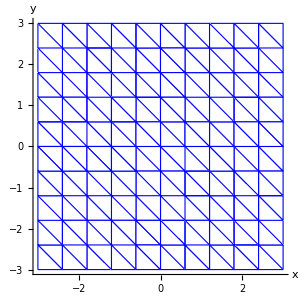
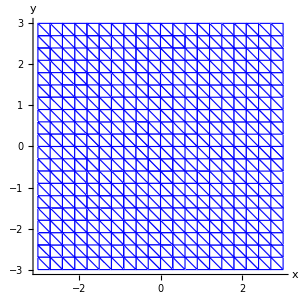
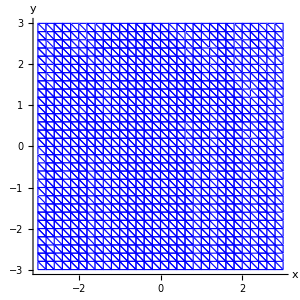
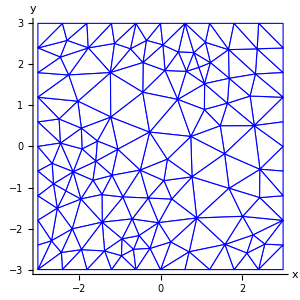
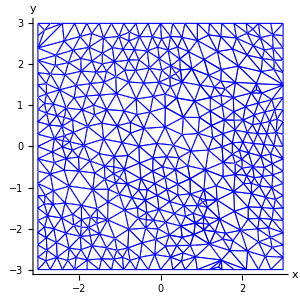
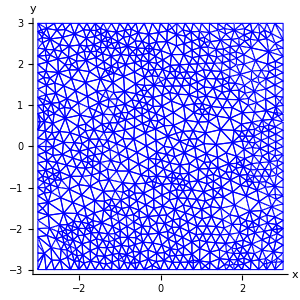
| 10 | 20 | 30
Regular mesh | -Graphics- | -Graphics- | -Graphics-
Iregular mesh | -Graphics- | -Graphics- | -Graphics-

```mathematica
dir=$HomeDirectory;

case="_regular"

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"10.dat"}],"Data"];
mesh10=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"20.dat"}],"Data"];
mesh20=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"30.dat"}],"Data"];
mesh30=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

case="_distorted"
tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"10.dat"}],"Data"];
mesh10dis=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"20.dat"}],"Data"];
mesh20dis=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"30.dat"}],"Data"];
mesh30dis=Graphics[ParallelTable[{EdgeForm[Blue],White,Polygon[parse2D[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

textstyle={TextAlignment->Center,FontFamily->"Times New Roman",FontSize->18}
Grid[Transpose[
{{"",Rotate[Style["Regular mesh",Evaluate[textstyle]],π/2],Rotate[Style["Iregular mesh",Evaluate[textstyle]],π/2]},
{Style["10",Evaluate[textstyle]],mesh10,mesh10dis},
{Style["20",Evaluate[textstyle]],mesh20,mesh20dis},
{Style["30",Evaluate[textstyle]],mesh30,mesh30dis}}],
Spacings->{{1,1,1,1}*0.5,{0,0,0,0}},
Frame->All]
```

```mathematica
dir=$HomeDirectory;
case="_distorted"
tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"10.dat"}],"Data"];
fL10=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]]

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_pseudo_quad"<>case<>"10.dat"}],"Data"];
fQ10=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"20.dat"}],"Data"];
fL20=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_pseudo_quad"<>case<>"20.dat"}],"Data"];
fQ20=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_linear"<>case<>"30.dat"}],"Data"];
fL30=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];

tmp=Import[FileNameJoin[{dir,"/output/peaksFunction_pseudo_quad"<>case<>"30.dat"}],"Data"];
fQ30=Graphics3D[ParallelTable[{EdgeForm[None],Polygon[parse[tmp[[i]]]]},{i,1,Length[tmp]}]
,Evaluate[style],Evaluate[plot3Doption]];
```

_distorted

-Graphics3D-

```mathematica
textstyle={TextAlignment->Center,FontFamily->"Times New Roman",FontSize->18}
Grid[Transpose[
{{"",Rotate[Style["Linear Interpolation",Evaluate[textstyle]],π/2],Rotate[Style["Pseudo-Quadratic Interpolation",Evaluate[textstyle]],π/2]},
{Style["10\n",Evaluate[textstyle]],fL10,fQ10},
{Style["20\n",Evaluate[textstyle]],fL20,fQ20},
{Style["30\n",Evaluate[textstyle]],fL30,fQ30}}],
Spacings->{{1,1,1,1}*0.5,{0,-3.5,-2,-1}},
Frame->All]
```

{TextAlignment→Center,FontFamily→Times New Roman,FontSize→18}

| 10
 | 20
 | 30

Linear Interpolation | -Graphics3D- | -Graphics3D- | -Graphics3D-
Pseudo-Quadratic Interpolation | -Graphics3D- | -Graphics3D- | -Graphics3D-

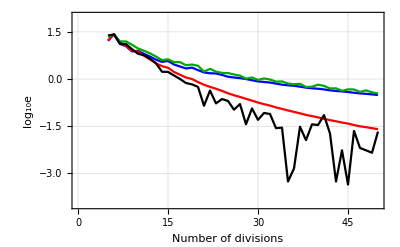
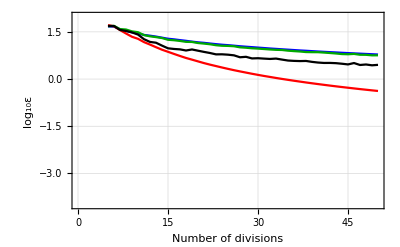
| 
-Graphics- | -Graphics-

```mathematica
dir=$HomeDirectory;
id="_regular";
dataLinear=Import[FileNameJoin[{dir,"output","peaks_integral_linear"<>id<>".dat"}],"Data"];
dataPseudoQuad=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad"<>id<>".dat"}],"Data"];
dataOriginal=Import[FileNameJoin[{dir,"output","peaks_integral_original"<>id<>".dat"}],"Data"];
dataLinearError=Import[FileNameJoin[{dir,"output","peaks_integral_linear_error"<>id<>".dat"}],"Data"];
dataPseudoQuadError=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad_error"<>id<>".dat"}],"Data"];

id="_distorted";
dataLinearIrregular=Import[FileNameJoin[{dir,"output","peaks_integral_linear"<>id<>".dat"}],"Data"];
dataPseudoQuadIrregular=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad"<>id<>".dat"}],"Data"];
dataOriginalIrregular=Import[FileNameJoin[{dir,"output","peaks_integral_original"<>id<>".dat"}],"Data"];
dataLinearIrregularError=Import[FileNameJoin[{dir,"output","peaks_integral_linear_error"<>id<>".dat"}],"Data"];
dataPseudoQuadIrregularError=Import[FileNameJoin[{dir,"output","peaks_integral_pseudo_quad_error"<>id<>".dat"}],"Data"];

colors={Blue,Red,Darker[Green],Black};

trueIntegral=114.09555552416919;

fig=Grid[{
{LineLegend[colors,Style[#,FontFamily->"Times",FontSize->15]&/@{"Linear Interpolation on Regular Mesh","Pseudo-Quadratic Interpolation on Regular Mesh","Linear Interpolation on Irregular Mesh","Pseudo-Quadratic Interpolation on Irregular Mesh"},LegendFunction->"Frame"],SpanFromLeft},
{
(*fig0=ListPlot[
{{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataLinear,
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataPseudoQuad,
(*{#1,#2}&@@@dataOriginal,*)
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataLinearIrregular,
{#1,Log10[Norm[(trueIntegral-#2)/trueIntegral]]}&@@@dataPseudoQuadIrregular}
,GridLines->Automatic
,FrameLabel->framelabel["Number of divisions","SubscriptBox[StyleBox[\"e\",FontSlant->\"Italic\"], \"lin\"], SubscriptBox[StyleBox[\"e\",FontSlant->\"Italic\"], \"pq\"]"]
,PlotRange->{Automatic,{-6,0}}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
],*)
fig1=ListPlot[
{{#1,Log10@Norm[trueIntegral-#2]}&@@@dataLinear,
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataPseudoQuad,
(*{#1,#2}&@@@dataOriginal,*)
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataLinearIrregular,
{#1,Log10@Norm[trueIntegral-#2]}&@@@dataPseudoQuadIrregular}
,PlotStyle->colors
,GridLines->Automatic
,FrameLabel->framelabel["Number of divisions","log_10e"]
,PlotRange->{Automatic,{-4,2}}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
],
fig2=ListPlot[
{{#1,Log10@#2}&@@@dataLinearError,
{#1,Log10@#2}&@@@dataPseudoQuadError,
{#1,Log10@#2}&@@@dataLinearIrregularError,
{#1,Log10@#2}&@@@dataPseudoQuadIrregularError}
,PlotStyle->colors
,GridLines->Automatic
(*,PlotLegends->Placed[{"Regular Linear","Regular Pseudo-Quad","Irregular Linear","Irregular Pseudo-Quad"},Right]*)
,PlotRange->{Automatic,{-4,2}}
,FrameLabel->framelabel["Number of divisions","log_10ε"]
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
]}
}]
(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/pseudo_quad_integration_accuracy.png",fig,ImageResolution->200]
Export["pseudo_quad_integration_accuracy.png",fig,ImageResolution->200]*)
```

```mathematica
(*toFit[d_]:=d^(1.2)*)Manipulate[
Module[{},
toFit1[d_]:=(d-sa)^(a)+sa;
toFit2[d_]:=(d-sb)^(b)+sb;
(*toFit[d_]:=d*)
Row@{
ListPlot[
{{#1,Log10@#2}&@@@dataLinearError,
{#1,Log10@#2}&@@@dataPseudoQuadError,
{#1,Log10@#2}&@@@dataLinearIrregularError,
{#1,Log10@#2}&@@@dataPseudoQuadIrregularError,
{toFit1@#1,Log10@#2}&@@@dataPseudoQuadError,
{toFit2@#1,Log10@#2}&@@@dataPseudoQuadIrregularError}
,PlotRange->{{0,150},{-1,2}}
,PlotLabel->{"a",a,"b",b,"sa",sa,"sb",sb}
,Evaluate[plot2Doption]
,Epilog->{Line[{{0,trueIntegral},{100,trueIntegral}}]}
]}
],{a,1.64,2.,0.01},{b,1.2,2.,0.01},{sa,6,30,1},{sb,0,30,1}
]
```

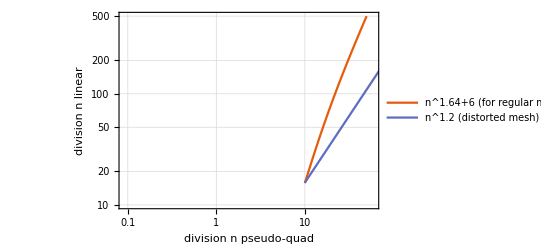

```mathematica
ListLogLogPlot[
{Table[{npseudo,(npseudo-6)^(1.64)+6} ,{npseudo,10,100,1}],
Table[{npseudo,(npseudo)^(1.2)} ,{npseudo,10,100,1}](*,
Table[{npseudo,2.*(npseudo)} ,{npseudo,10,100,1}]*)}
,PlotLegends->{"n^1.64+6 (for regular mesh)","n^1.2 (distorted mesh)"}
,PlotRange->{{0,60},{10,500}}
,Evaluate[plot2Doption]
,GridLines->All
,FrameLabel->framelabel["division n pseudo-quad","division n linear"]
]
```